# Pinball Path Aproximation

```mathematica
Farey[n_]:=Join[{0},Union[Table[i/j,{j,n},{i,j-1}]//Flatten],{1}]
Mediant[a_,b_]:=(Numerator[a]+Numerator[b])/(Denominator[a]+Denominator[b])
```

```mathematica
FareyCircle[n_,k_]:=Module[{T,F,kinf,ksup},T={}; F=Farey[n];kinf=k[[1]];ksup=k[[2]];
For[i=1,i≤Length[F],i++,
	For[j=1,j≤Length[F],j++, If[Abs[Numerator[F[[i]]]*Denominator[F[[j]]]- Numerator[F[[j]]]*Denominator[F[[i]]]]==1, 
		For[h=kinf,h≤ksup,h++, AppendTo[T,{Dashing[Tiny],Circle[{(F[[i]]+F[[j]])/2+h,0},Abs[F[[i]]-F[[j]]]/2,{0,Pi}]}] ] ] ]]; 
T=DeleteDuplicates[T]; 

AppendTo[T,Text[Style["1/0",Black,FontSize->8],{ksup+1-1/2^6,3/4}]];
AppendTo[T,Text[Style[ksup+2,Black,FontSize->8],{ksup+1,-1/8}]];
For[h=kinf,h≤ksup,h++,
AppendTo[T,{Dashing[Tiny],Line[{{h,3/4},{h,0},{h+1,0},{h+1,3/4}}]}];
AppendTo[T,Text[Style["1/0",Black,FontSize->8],{h+-1/2^6,3/4}]];  
AppendTo[T,Text[Style[h+1,Black,FontSize->8],{h,-1/8}]]; 
];
T]

FractionFarey[x_,n_]:=Module[{CF,a,b,piv,FF}, 
If[Element[x,Rationals],CF=ContinuedFraction[x],CF=ContinuedFraction[x,n]]; 
b=1; a=First[CF]; FF={a};
For[i=2,i≤Length[CF],i++,piv=a; a=b; b=piv; For[j=1,j≤CF[[i]],j++,If[i==2 &&j==1,a=a+b,a=Mediant[a,b]]]; AppendTo[FF,a]]; 
FF]
```

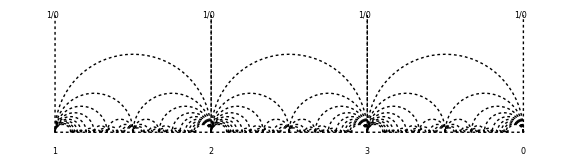

```mathematica
Graphics[FareyCircle[10,{0,2}],ImageSize->Large]
```

```mathematica
SemiCircle[t_,a_,b_]:= Module[{T},If[b>a,T={Thick,Red,Circle[{(a+b)/2,0},Abs[b-a]/2,{Pi,Pi-Pi*t}]},T={Thick,Red,Circle[{(a+b)/2,0},Abs[b-a]/2,{0,Pi*t}]}]; T]

SemiCirclesList[t_,L_]:=Module[{T,Tl},If[-1≤t≤1 ,
If[-1≤t≤0,T={Thick,Red,Line[{{First[L],3/4},{First[L],-3*t/4}}]},T={{Thick,Red,Line[{{First[L],3/4},{First[L],0}}]},SemiCircle[t,L[[1]],L[[2]]]}],
	T=Table[SemiCircle[1,L[[i]],L[[i+1]]],{i,1,Floor[t]}]; PrependTo[T,{Thick,Red,Line[{{First[L],3/4},{First[L],0}}]}] ; AppendTo[T,SemiCircle[t-Floor[t],L[[Floor[t]+1]],L[[Floor[t]+2]] ] ] ]; 
For[i=1,i≤Length[L],i++,AppendTo[T,Text[Style[Numerator[L[[i]]]/Denominator[L[[i]]],Red,FontSize->10],{L[[i]],-1/2^4}]]]; 
T=Union[T,FareyCircle[15,{First[L],First[L]}]]; 
Graphics[T,ImageSize->Full]]
```

```mathematica
Pinball[x_,n_]:= Manipulate[SemiCirclesList[t,FractionFarey[x,n]],{t,-1,Length[FractionFarey[x,n]]-1-0.001},ControlType->Animator,ControlPlacement->Bottom]
```

```mathematica
Pinball[GoldenRatio,12]
```